```mathematica
ClearAll["Global`*"];
(*Ciało wykonuje drgania harmoniczne wzdłuż dwóch kierunków prostopadłych do siebie zgodnie z równaniami:
X=A Sin(ωx t)
Y=A Sin(ωy t+δ)
 Sporządzić wykresy toru punktu drgającego dla następujących przypadków:
a) ωy=ωx;          δ=0,      δ=π/4,    δ=π/2,   δ=π 
	    b) ωy=(2/3)ωx;  δ=0,     δ=π/6,     δ=π/3,   δ=3 π/6,   δ=4 π/6 
		 c) ωy=(1/2)ωx;  δ=0,     δ=π/6,     δ=π/3,   δ=3 π/6,   δ=4 π/6 
		           d) ωy=(1/3)ωx;  δ=0,     δ=π/6,     δ=π/3,   δ=3 π/6,   δ=4 π/6 
			        e) ωy=(4/3)ωx    δ=0     δ=π/6      δ=π/3     δ=3 π/6    δ=4 π/6 *)
```

```mathematica
A=1;             (* m *)
```

```mathematica
tk=4×(2π)/ωy;
```

```mathematica
ωx=1;           (* rad/s *)
```

```mathematica
ωy=1;            (* rad/s *)
```

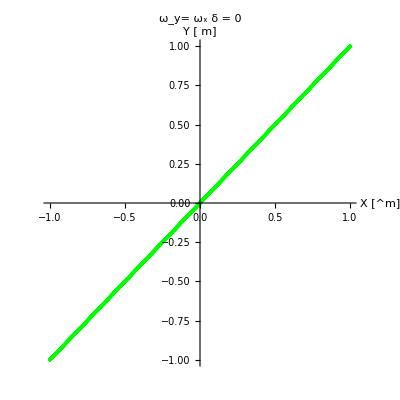

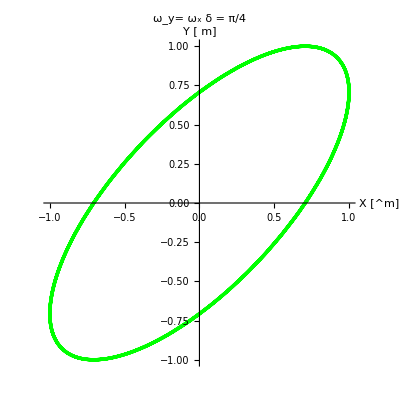

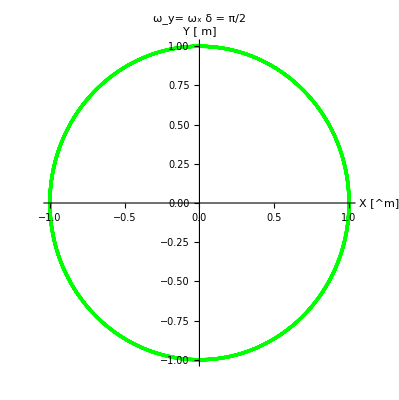

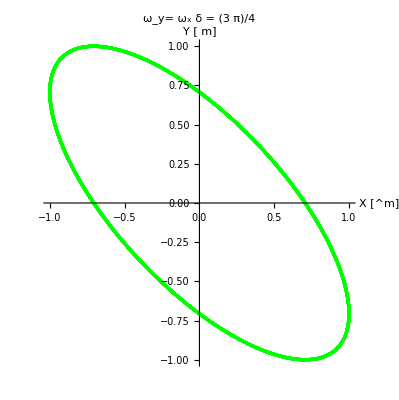

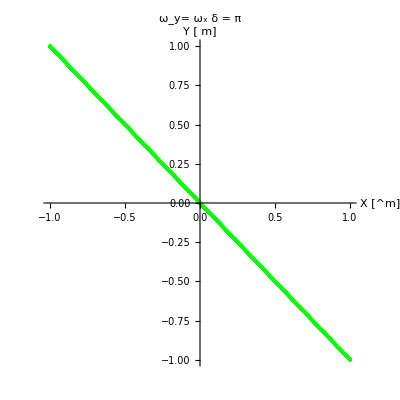

```mathematica
Do[rys1[δ_]=Print[ParametricPlot[{A×Sin[ωx×t],A×Sin[ωy×t+δ]},{t,0,tk}, PlotStyle->{{RGBColor[0,1,0],Thickness[0.006]}},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm["     ω_y= ω_x                                           δ = ``  ",δ],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],AxesLabel->{"X  [^m]","Y [ m]"}]],{δ,0,π,π/4}]
```

```mathematica
ωx=1;           (* rad/s *)
```

```mathematica
ωy=2/3;         (* rad/s *)
```

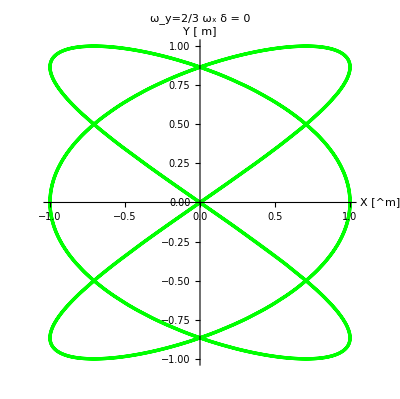

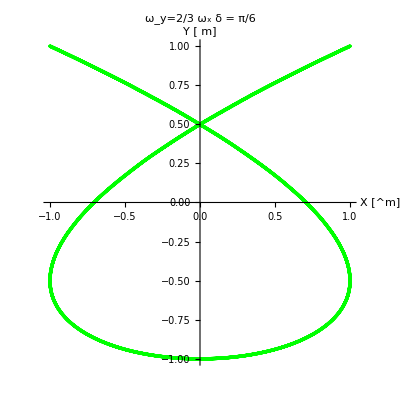

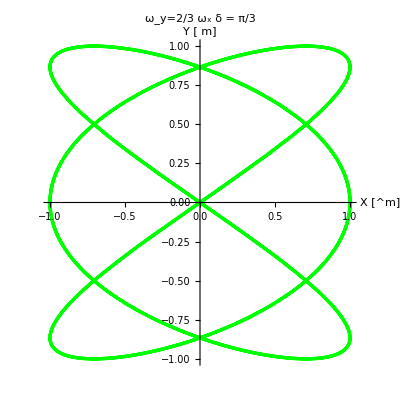

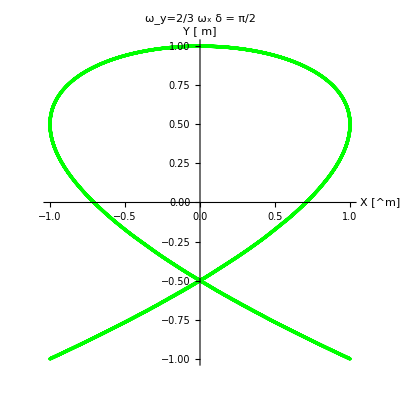

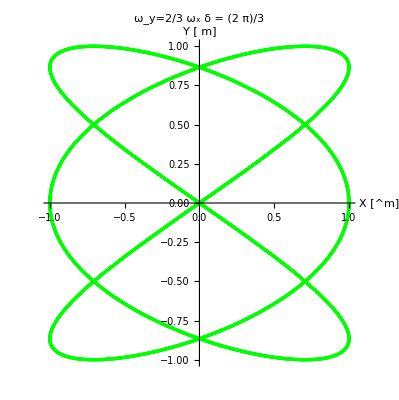

```mathematica
Do[rys2[δ_]=Print[ParametricPlot[{A×Sin[ωx×t],A×Sin[ωy×t+δ]},{t,0,tk}, PlotStyle->{{RGBColor[0,1,0],Thickness[0.006]}},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm["     ω_y=2/3 ω_x                                           δ = ``  ",δ],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],AxesLabel->{"X  [^m]","Y [ m]"}]],{δ,0,2/3×π,π/6}]
```

```mathematica
ωx=1;           (* rad/s *)
```

```mathematica
ωy=1/2;         (* rad/s *)
```

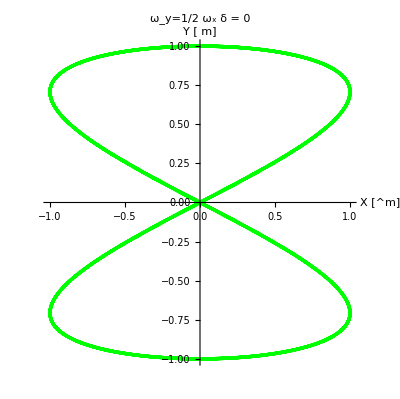

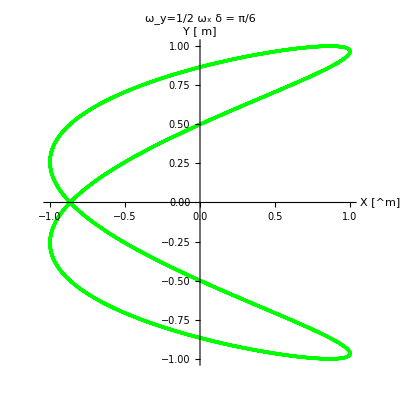

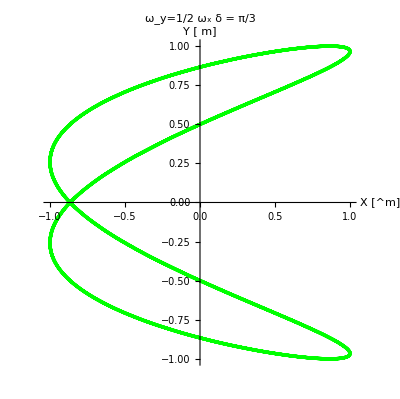

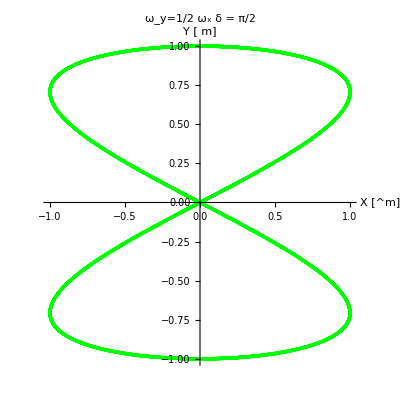

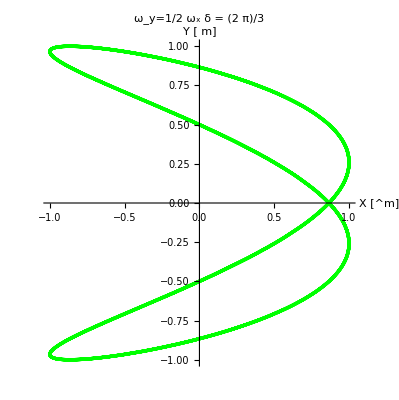

```mathematica
Do[rys3[δ_]=Print[ParametricPlot[{A×Sin[ωx×t],A×Sin[ωy×t+δ]},{t,0,tk}, PlotStyle->{{RGBColor[0,1,0],Thickness[0.006]}},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm["     ω_y=1/2 ω_x                                           δ = ``  ",δ],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],AxesLabel->{"X  [^m]","Y [ m]"}]],{δ,0,2/3×π,π/6}];
```

```mathematica
ωx=1;           (* rad/s *)
```

```mathematica
ωy=1/3;         (* rad/s *)
```

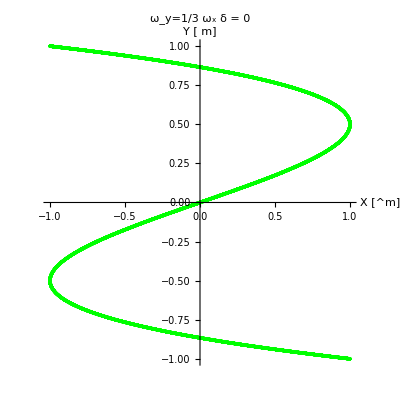

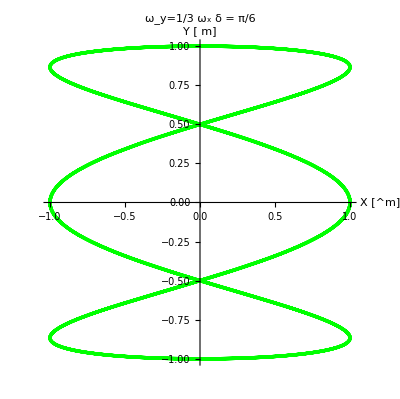

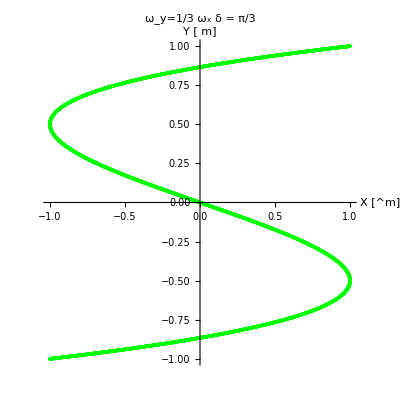

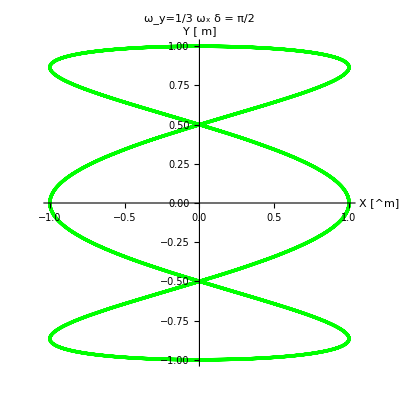

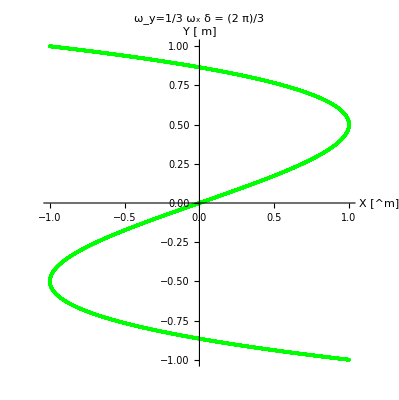

```mathematica
Do[rys4[δ_]=Print[ParametricPlot[{A×Sin[ωx×t],A×Sin[ωy×t+δ]},{t,0,tk}, PlotStyle->{{RGBColor[0,1,0],Thickness[0.006]}},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm["     ω_y=1/3 ω_x                                           δ = ``  ",δ],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],AxesLabel->{"X  [^m]","Y [ m]"}]],{δ,0,2/3×π,π/6}]
```

```mathematica
ωx=1;           (* rad/s *)
```

```mathematica
ωy=4/3;         (* rad/s *)
```

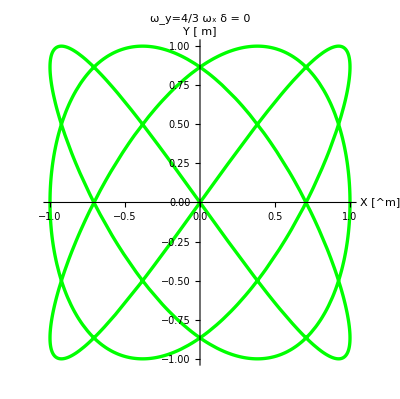

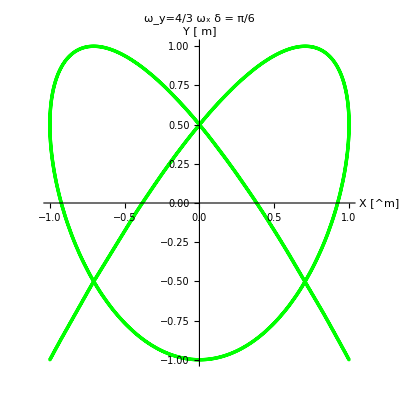

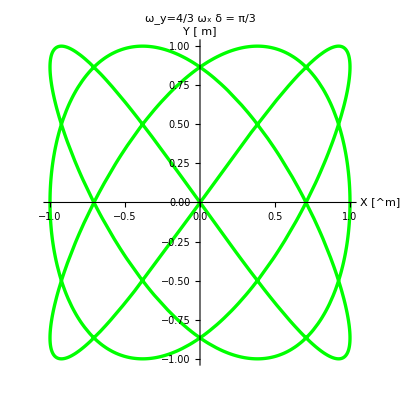

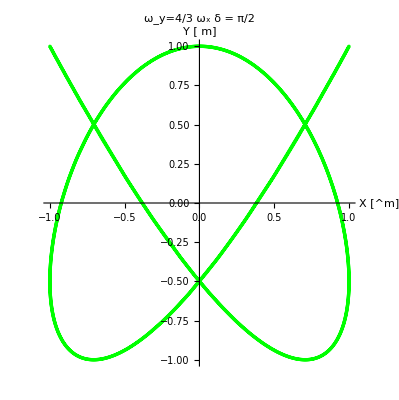

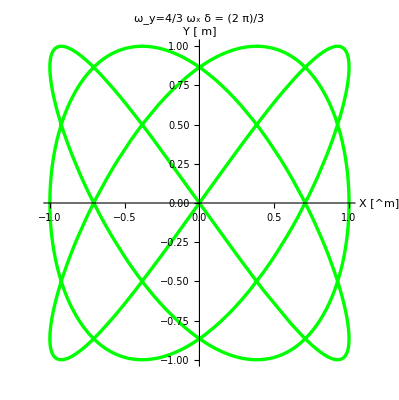

```mathematica
Do[rys5[δ_]=Print[ParametricPlot[{A×Sin[ωx×t],A×Sin[ωy×t+δ]},{t,0,tk}, PlotStyle->{{RGBColor[0,1,0],Thickness[0.006]}},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotLabel->StyleForm[StringForm["     ω_y=4/3 ω_x                                           δ = ``  ",δ],
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->10],AxesLabel->{"X  [^m]","Y [ m]"}]],{δ,0,2/3×π,π/6}]
```